## code Archived (Principle Directions/EigenVectors)

```mathematica
(* Clear@findSym;
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(* here we transpose the image data *)
{nx,ny}=Dimensions[imd];(* dimensions of the image *)
points=Tuples[{Range[nx],Reverse@Range[ny]}]; (* x-y coordinates on the image *)
weights=Flatten[imd]; (* vector of imagedata *)

centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(* here we calculate the x-y coordinate of the center of mass *)

pointsCom=(Subtract[#,centerOfMass]&/@points) weights; (* we subtract from each point the center of mass. This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids. We multiply this resulting matrix with the intensity vector. This gives us a vector consisting of two coordinates which are x y displacments from centroid * intensity for each point in the grid *)

diag=Total[(#.#)&/@pointsCom]; (* sum of the {x,y}.{x,y} from above. gives a single values *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}]; (* inertia *)

{v1,v2}=Eigenvectors[inertia]; (* extracting eigenvectors from inertia *)
(* Print["center of Mass: ", centerOfMass,"\n","pt1 : ",v1 + centerOfMass,"\n","pt2 : ",v2 + centerOfMass]; *)

(* display *)
If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]];
{centerOfMass,v1,v2}
] *)
```

```mathematica
(* Clear@maskToRegion;
maskToRegion[mask_]:= Block[{pixelvaluepos,tour,pixelposordered},
pixelvaluepos= PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[pixelvaluepos];
pixelposordered = Part[pixelvaluepos,tour];
{pixelposordered,BoundaryMeshRegion[N@pixelvaluepos,Line@tour]}
] *)
```

```mathematica
(* Clear@bisectMask;
bisectMask[mask_,option_:False]:= Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,temp,pt1,pt2,list,
trimList,npixelordered,nf, ptslocation,firstPreMask,secondPreMask,dim},
dim=First@ImageDimensions[mask];
{centerofMass,v1,v2}=findSym[mask];
{pixelordered,ℛ1}=maskToRegion[mask];
ℛ2=InfiniteLine[{centerofMass,centerofMass+v1}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:> arg]&);

trimList[ls_]:= Module[{p=ls,pairs,firstelem = First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt1,pt2}=trimList[list]/.trimList[arg__]:> arg;

If[option,temp=Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,
Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]
]
];

npixelordered = N@pixelordered;
nf=Nearest[npixelordered];
ptslocation=Flatten@Position[npixelordered,Flatten@nf[pt1]|Flatten@nf[pt2]];

firstPreMask=PadRight[#,Length@#+1,#]&@Part[pixelordered,First@ptslocation;;Last@ptslocation]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;

secondPreMask=Join[pixelordered[[;;First@ptslocation+1]],pixelordered[[Last@ptslocation+1;;]]]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;

Switch[option,True,Join[{temp},{centerofMass},pt1,pt2],_,Join[{centerofMass},pt1,pt2]]
]
*)
```

## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\96 hours\\principleDir.m"
```

## 1. Mean Intensity of E-Cadherin

```mathematica
(*  contrast, elongation and fourier elliptic descriptors  *)
```

```mathematica
img=ImageAdjust@Import@"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\9\\img_000000000_Empty_000.tif";
ecad = ImageAdjust@Import@"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\9\\imagecorrMinusMean9.tiff";
mask =Import@"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\9\\Mask2.tif";
```

```mathematica
HighlightImage[ecad,mask,ImageSize->Medium]
```

-Graphics-

```mathematica
HighlightImage[img,mask,ImageSize->Medium]
```

-Graphics-

```mathematica
meanI=ImageMeasurements[ecad,"MeanIntensity",Masking-> mask] (* mean intensity of the image to which the mask is applied *)
```

0.415603

## 2. Aggregate elongation metric

```mathematica
elongation=ComponentMeasurements[mask,"Elongation"][[1,2]]
```

0.110634

## 3. Contrast of E-Cadherin along pseudo-axes of symmetry

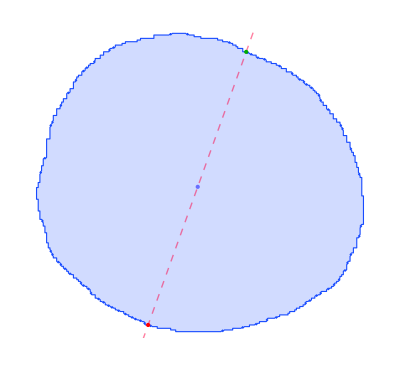
{-Graphics-,{839.149,355.418},{809.561,273.},{868.058,435.942}}

```mathematica
{symmb,centroid,pt1,pt2}=bisectMask[mask,True]
```

## 4. r(θ) and contrast(θ)

```mathematica
boundary=PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[boundary];
boundaryc=Part[boundary,tour];
nF=Nearest[boundaryc];
```

```mathematica
ℛ1=BoundaryMeshRegion[boundary,Line@tour];
```

```mathematica
ℛ2=InfiniteLine[{centroid,pt1}];
```

```mathematica
intersections=Cases[RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1],_Point]/.Point[{x_}]:> x;
```

```mathematica
div=5;
```

```mathematica
rotationTransform=RotationTransform[div Degree,centroid]
```

TransformationFunction[(0.996195 | -0.0871557 | 34.1699
0.0871557 | 0.996195 | -71.7842
0. | 0. | 1.)]

```mathematica
pts=Rest@NestList[rotationTransform,pt1,360/div];
```

```mathematica
arrow=Arrow[{centroid,#}]&/@pts;
```

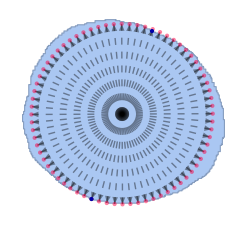

```mathematica
Show[ℛ1,Graphics[{{Arrowheads-> Small,Thick,Dashed,XYZColor[0,0,0,0.4],arrow},
{XYZColor[1,0,0,0.5],PointSize[Medium],Point@pts},{Darker@Blue,PointSize[Large],Point@intersections}}]]
```

```mathematica
infinitelines=InfiniteLine[{centroid,#}]&/@pts;
(* contour= MeshPrimitives[ℛ1,1];
surfacepts=(x↦Cases[RegionIntersection[x,#]&/@contour,_Point])/@infinitelines/.Point[{x_}]:> x; *)
```

```mathematica
contour = Polygon@boundaryc;
(*surfacepts=(x↦RegionIntersection[x,contour])/@infinitelines/.Point[x_]:>x; *)
```

```mathematica
surfacepts=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],contour,#}]]&/@infinitelines;
```

```mathematica
pos=Position[surfacepts,_?(Length@#>2&),{1}];
```

```mathematica
surfacepts2=MapAt[Sequence@@TakeLargestBy[Permutations[#,{2}],EuclideanDistance[#[[1]],#[[2]]]&,1]&,surfacepts,pos];
```

```mathematica
surfacepts3=Part[surfacepts2,All;;Length[surfacepts2]/2];
```

```mathematica
aggregatesymbstruct=Show[
HighlightMesh[ℛ1,Style[1,Black],Background->None],Graphics[{{Arrowheads-> Small,Thick,Dashed,XYZColor[0,0,0,0.4],arrow},Darker@Blue,PointSize[Medium],
Point@Flatten[surfacepts3,1],Darker@Green,Point@centroid,XYZColor[1,0,0,0.5],PointSize[Medium],Point@pts}]
];
```

```mathematica
θ = Array[#&,360/div,{0,2π}];
```

```mathematica
Clear[contrast,r,p];
```

```mathematica
p/:r[p]:= Join[#[[;;,1]],#[[;;,2]]]&@Map[EuclideanDistance[centroid,#]&,surfacepts3,{2}];
```

```mathematica
plot1=ListPlot[{f=Thread[{θ,r[p]}],f},Joined->{True,False},PlotStyle-> {{Thick,Dashed},{Black,PointSize[Medium]}},
AxesLabel->(Style[#,{Black,Bold,FontSize->12}]&/@{"θ (rad)","r[θ]"}),PlotLabel->Style["Centroid to boundary distance",{Bold,Black,FontFamily->"Courier"}]];
```

```mathematica
constrastTheta[boundarycoord_,image_,surfacepts_]:=With[{nearest=nF,imagesize = 1024},
Block[{ptb1,ptb2,pos1,pos2,fmask,smask,r1,r2,contrast},
({ptb1,ptb2}=First@*nearest/@#;
{pos1,pos2} = Position[boundarycoord,ptb1|ptb2][[;;2]];
fmask = PadRight[#,Length@#+1,#]&@Part[boundarycoord,First[pos1];;First[pos2]]//Graphics[{White,Line@#},PlotRange->{{0,imagesize},{0,imagesize}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{imagesize},{imagesize}}]&//FillingTransform@*Binarize;
smask=Join[boundarycoord[[;;First@pos1+1]],boundarycoord[[First@pos2+1;;]]]//Graphics[{White,Line@#},PlotRange->{{0,imagesize},{0,imagesize}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{imagesize},{imagesize}}]&//FillingTransform@*Binarize;
{r1,r2}=ImageMeasurements[image*#,"TotalIntensity",Masking->#]&/@{fmask,smask};
contrast=(Abs[Subtract@@#]/Total[#])&@{r1,r2})&/@surfacepts
]
]
```

```mathematica
p/:contrast[p]=constrastTheta[boundaryc,ecad,surfacepts3];
```

```mathematica
plot2=ListPlot[{g=Thread[{Take[θ,Length[θ]/2],contrast[p]}],g},Joined->{True,False},
PlotStyle-> {{Thick,Dashed},{Black,PointSize[Medium]}},
AxesLabel->(Style[#,{Black,Bold,FontSize->12}]&/@{"θ (rad)","f[θ]"}),
PlotLabel->Style["Contrast(θ)",{Bold,Black,FontFamily->"Courier"}]];
```

```mathematica
boundingbox=Values@@ComponentMeasurements[mask,"BoundingBox"];
```

```mathematica
aggregatesym=Show[ecad*mask,HighlightMesh[ℛ1,{Style[2,None],Style[1,{Black}]}],Graphics[{Dashed,Thick,Pink,infinitelines[[All;;All;;3]],Lighter@Cyan,PointSize[Medium],Point@Flatten[surfacepts3,1],Red,PointSize[Large],Point@centroid}]]//ImageTrim[#,boundingbox]&//Rasterize[#,"Image",ImageResolution->500]&;
```

```mathematica
GraphicsRow[{aggregatesymbstruct,aggregatesym,plot1,plot2},ImageSize->Full]
```

-Graphics-

```mathematica
mesh=HighlightMesh[ℛ1,{Style[2,None],Style[1,{LightGreen}]}];
```

```mathematica
If[ValueQ[mesh]&&ValueQ[infinitelines],
Manipulate[
GraphicsRow[
{Show[ecad*mask,mesh,
Graphics[{Dashed,White,infinitelines[[i]],PointSize[Large],Red,Point@centroid,
Yellow,Point@surfacepts3[[i]]}]]//ImageTrim[#,boundingbox]&,
Show[plot2,Graphics[{XYZColor[0,0,1,0.6],PointSize[0.07],Point[g[[i]]]}]]}
],{i,1,Length[infinitelines]/2,1},
SaveDefinitions->True
]
]
```

```mathematica
diameter=Plus@@Partition[r[p],Length[r[p]]/2];
```

```mathematica
MinMax[contrast[p]]
```

{0.000023301,0.0269276}

```mathematica
MinMax@diameter
```

{171.844,195.959}

```mathematica
(*
Show[ListPlot[k=Thread[{diameter,contrast[p]}],ColorFunction->"Rainbow",PlotStyle->Dashed,Joined->True],ListPlot[k,PlotStyle->Black],AxesLabel->(Style[#,{Black,Bold,FontSize->12}]&/@{"r[θ]","f[θ]"}),PlotLabel->Style["Contrast(θ)Vs r[θ]",{Bold,Black,FontFamily->"Courier"}]]
*)
```

### output results

```mathematica
{meanI,elongation,MinMax@contrast[p]}
```

{0.415603,0.110634,{0.000023301,0.0269276}}

## results

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\96 hours\\saved data.mx";
```

```mathematica
Style[TableForm[chipos,TableHeadings->{Range[Length@chipos],{"<I_chipos>","ϵ", "Contrast_(Min/Max)"}}],Small];
```

```mathematica
Style[TableForm[chineg,TableHeadings-> {Range[Length@chineg],{"<I_chiNeg>","ϵ", "Contrast_(Min/Max)"}}],Small];
```

```mathematica
{chiposd3,chinegd3} =Map[{#1,#2,#3[[2]]}&@@#&,#]&/@{chipos,chineg};
```

```mathematica
Length/@{chinegd3,chiposd3}
```

{20,37}

```mathematica
cF[cedf_: "BoxWhisker",o:OptionsPattern[]]:=Dynamic@With[{col=CurrentValue["Color"]},{ChartElementDataFunction[cedf,o][##],ListPlot[Thread[{Mean[#[[1]]],#2}],PlotStyle->XYZColor[0,0,0,0.25],PlotMarkers->#3[[1]]][[1]]}]&
```

```mathematica
MapThread[BoxWhiskerChart[Thread[{chiposd3[[All,#1]],chinegd3[[All,#1]]}->{"●","●"}],ChartElementFunction->cF[],ImageSize->Medium,ChartStyle->{#2,Lighter@#2},ChartLabels->(Style[#,Bold,Italic,GrayLevel[0.25],FontSize->13]&/@{"Chi +","Chi -"}),PlotLabel->#3,FrameTicksStyle->Directive[Black,18]]&,{{1,2,3},{XYZColor[0.3,0.3,0.9],XYZColor[1,0,0,0.7],XYZColor[0,0.36,0.39]},Style[#,Italic,GrayLevel[0.25],FontSize->15]&/@{"Mean Intensity","Elongation","Polarization"}}]//GraphicsRow
```

-Graphics-